```mathematica
CompletedFormula[form_,edge_]:=Map[SymbolReplace[#,edge]&,form]
```

```mathematica
SymbolReplace[v14x3x5x67,1<->2]
```

v124x3x5x67

```mathematica
SymbolToEdges[{v124x3x5x67}]
```

{1<->2→{RGBColor[0, Rational[2, 3], 0],Thickness[Large]},1<->4→{RGBColor[0, Rational[2, 3], 0],Thickness[Large]},2<->4→{RGBColor[0, Rational[2, 3], 0],Thickness[Large]},3→{RGBColor[0, Rational[2, 3], 0]},5→{RGBColor[0, Rational[2, 3], 0]},6<->7→{RGBColor[0, Rational[2, 3], 0],Thickness[Large]}}

```mathematica
SymbolToVertices[{v124x3x5x67}]
```

{3→{RGBColor[0, Rational[2, 3], 0]},5→{RGBColor[0, Rational[2, 3], 0]}}

```mathematica
SymbolToEdges[s_]:=Block[{result={}},
result=Flatten[
Table[
With[{sets=SymbolToSets[symbol]},
Table[
Table[UndirectedEdge[e[[1]],e[[2]]]->{Darker[Green],Thick}
,{e,Subsets[bucket,{2}]}
]
,{bucket,Select[sets,Length[#]!=1&]}]
],
{symbol,s}
]
]
]
```

```mathematica
SymbolToVertices[s_]:=Block[{result={}},
result=Flatten[
Table[
With[{sets=SymbolToSets[symbol]},
Table[
bucket[[1]]->{Darker[Green],Large}
,{bucket,Select[sets,Length[#]==1&]}]
],
{symbol,s}
]
]
]
```

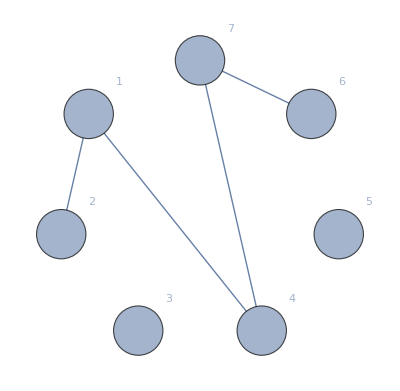
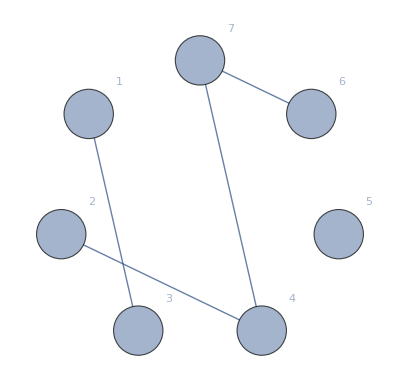
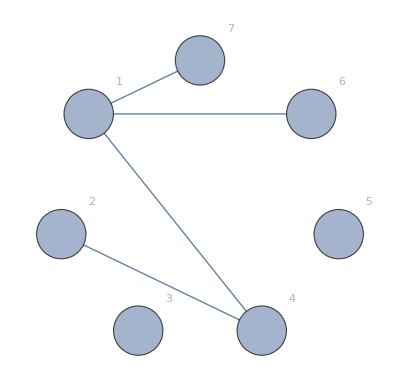
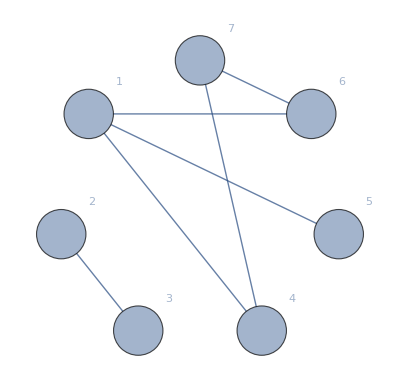
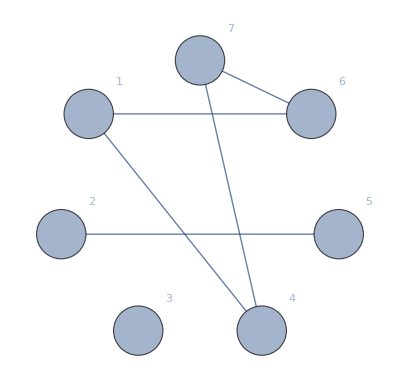
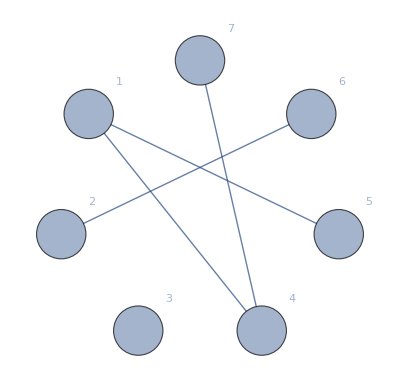
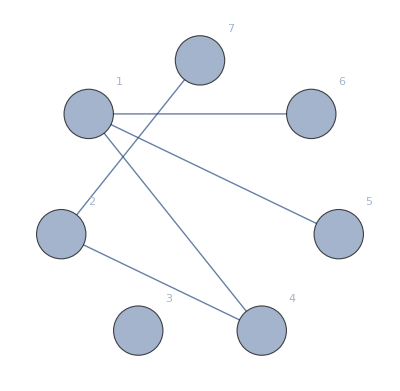
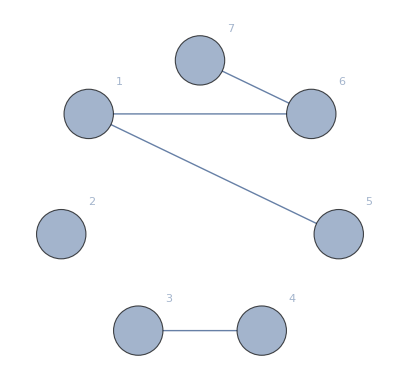
{-Graphics-{1<->2},-Graphics-{1<->3},-Graphics-{1<->7},-Graphics-{2<->3},-Graphics-{2<->5},-Graphics-{2<->6},-Graphics-{2<->7},-Graphics-{3<->4},-Graphics-{3<->5},-Graphics-{3<->6},-Graphics-{3<->7},-Graphics-{4<->5},-Graphics-{4<->6},-Graphics-{5<->6},-Graphics-{5<->7}}

```mathematica
With[{g=ReadGrof[5]},
Table[
With[{
full=FindFullFormula[g],
contr=GContract[g,e]},
With[{h=GraphComplement[contr]},
With[{contrform=FindFullFormula4[contr]},

Framed[Labeled[Graph[Range[VertexCount[g]],Append[EdgeList[h],e],VertexLabels->"Name",GraphLayout->"CircularEmbedding",EdgeStyle->Join[{e->{Red,Thick}},SymbolToEdges[contrform]],VertexSize->Large,VertexStyle->Join[{e[[1]]->{Red,Thick},e[[2]]->{Red,Thick}},SymbolToVertices[contrform]]],{e}]]
]
]
],{e,EdgeList[g]}]
]
```

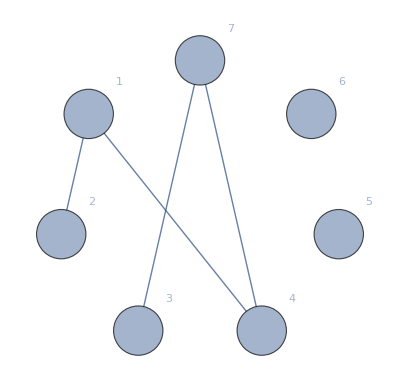
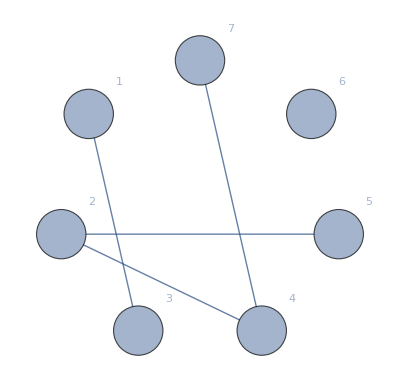
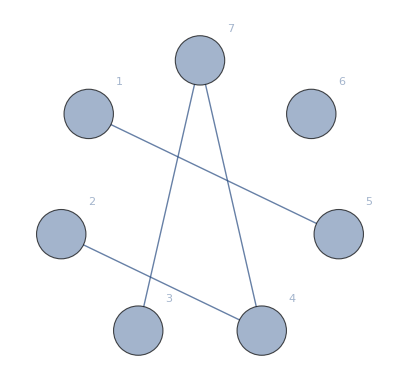
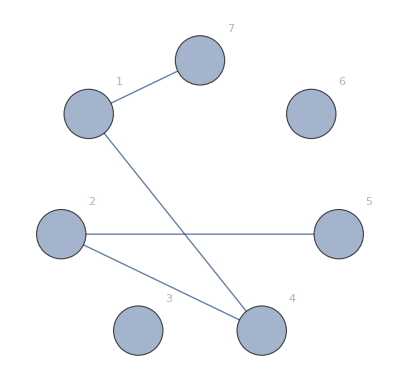
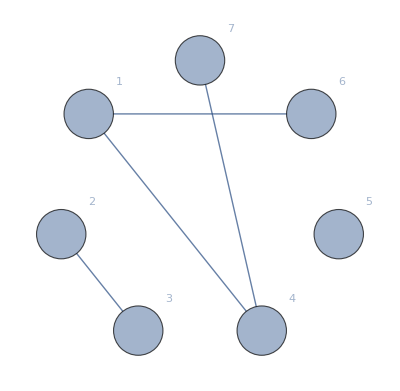
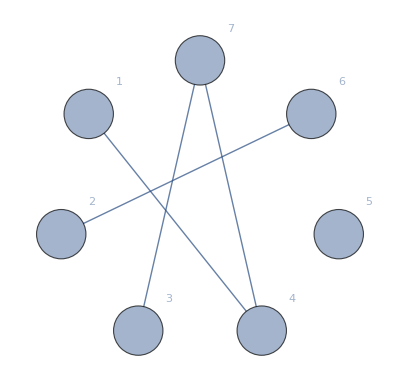
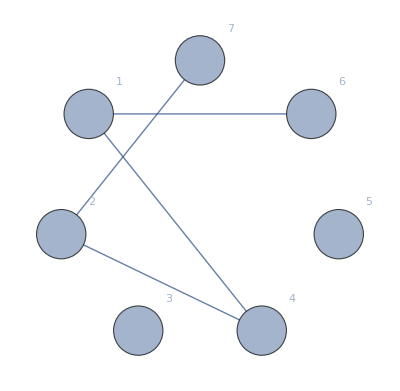
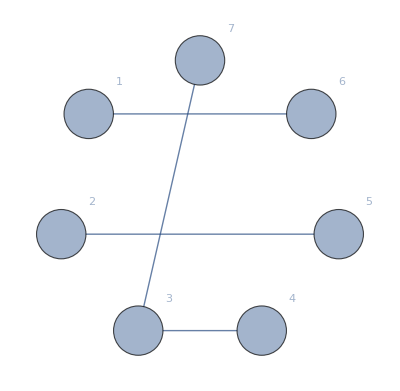
{-Graphics-{1<->2},-Graphics-{1<->3},-Graphics-{1<->5},-Graphics-{1<->7},-Graphics-{2<->3},-Graphics-{2<->6},-Graphics-{2<->7},-Graphics-{3<->4},-Graphics-{3<->5},-Graphics-{3<->6},-Graphics-{4<->5},-Graphics-{4<->6},-Graphics-{5<->6},-Graphics-{5<->7},-Graphics-{6<->7}}

```mathematica
With[{g=ReadGrof[6]},
Table[
With[{
full=FindFullFormula[g],
contr=GContract[g,e]},
With[{h=GraphComplement[contr]},
With[{contrform=FindFullFormula4[contr]},

Framed[Labeled[Graph[Range[VertexCount[g]],Append[EdgeList[h],e],VertexLabels->"Name",GraphLayout->"CircularEmbedding",EdgeStyle->Join[{e->{Red,Thick}},SymbolToEdges[contrform]],VertexSize->Large,VertexStyle->Join[{e[[1]]->{Red,Thick},e[[2]]->{Red,Thick}},SymbolToVertices[contrform]]],{e}]]
]
]
],{e,EdgeList[g]}]
]
```

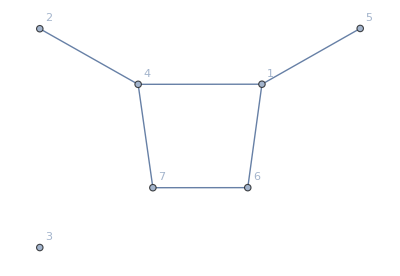

```mathematica
Graph[Fold[GraphUnion,With[{g=ReadGrof[5]},
Table[
With[{
full=FindFullFormula[g],
contr=GContract[g,e]},
With[{h=GraphComplement[contr]},
Graph[Range[VertexCount[g]],EdgeList[h],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]
]
],{e,EdgeList[g]}]
]],VertexLabels->"Name"]
```

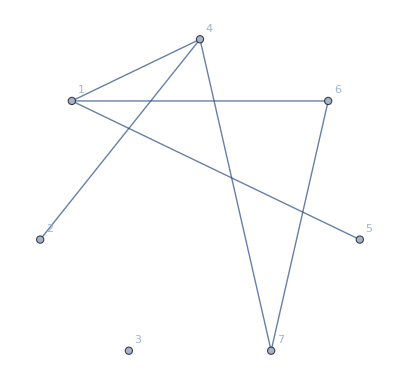

```mathematica
GraphComplement[ReadGrof[5],VertexLabels->"Name"]
```

```mathematica
SymbolToSets
```

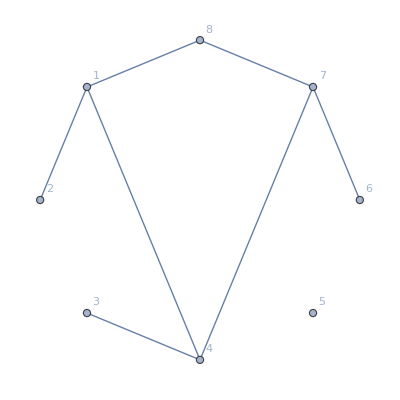
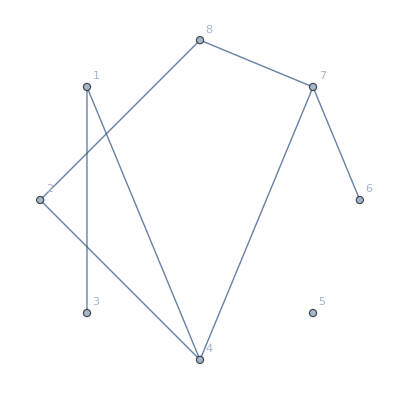
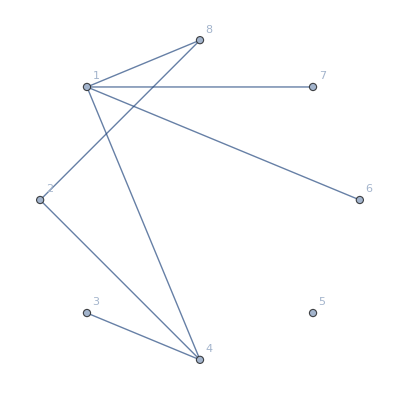
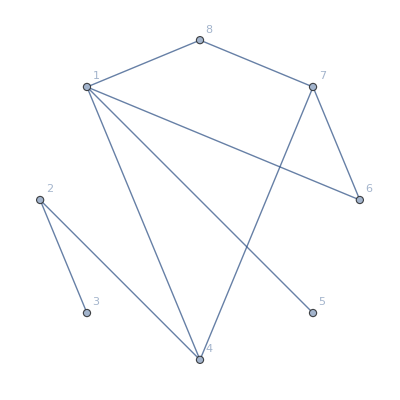
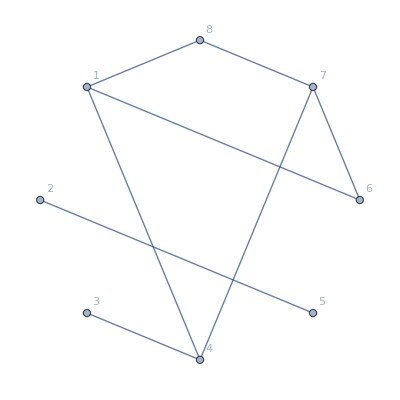
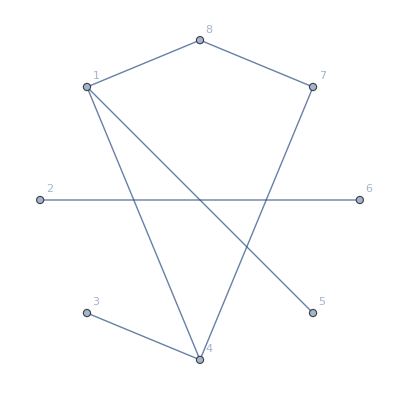
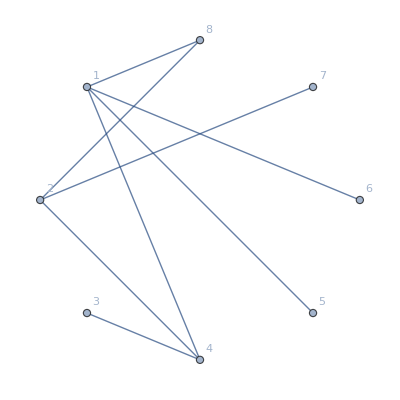
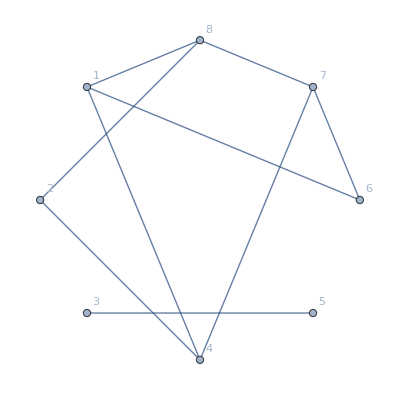
{-Graphics-{1<->2,{v128x34x5x67}},-Graphics-{1<->3,{v134x28x5x67}},-Graphics-{1<->7,{v167x28x34x5}},-Graphics-{2<->3,{v18x234x5x67,v16x234x5x78,v15x234x6x78,v15x234x67x8}},-Graphics-{2<->5,{v18x25x34x67,v16x25x34x78}},-Graphics-{2<->6,{v15x26x34x78}},-Graphics-{2<->7,{v16x278x34x5,v15x278x34x6}},-Graphics-{3<->5,{v14x28x35x67,v18x24x35x67,v16x24x35x78,v16x28x35x47}},-Graphics-{3<->6,{v15x24x36x78,v15x28x36x47}},-Graphics-{3<->7,{v16x28x347x5,v15x28x347x6}},-Graphics-{3<->8,{v15x24x38x67}},-Graphics-{4<->5,{v145x28x3x67}},-Graphics-{4<->6,{v15x28x3x467}},-Graphics-{4<->8,{v15x248x3x67}},-Graphics-{5<->6,{v156x2x34x78,v156x24x3x78,v156x28x3x47,v156x28x34x7}},-Graphics-{5<->7,{v16x28x34x57}},-Graphics-{5<->8,{v158x2x34x67,v158x24x3x67}},-Graphics-{6<->8,{v15x2x34x678,v15x24x3x678}}}

```mathematica
With[{g=ReadGrof[10]},
Table[
With[{
full=FindFullFormula[g],
contr=GContract[g,e]},
With[{h=GraphComplement[contr]},
Framed[Labeled[Graph[Range[VertexCount[g]],Append[EdgeList[h],e],VertexLabels->"Name",GraphLayout->"CircularEmbedding",EdgeStyle->Join[{e->{Red,Thick}},Map[#->{Darker[Green],Thick}&,SymbolToEdges[First[FindFullFormula4[contr]]]]]],{e,CompletedFormula[FindFullFormula4[contr],e]}]]
]
],{e,EdgeList[g]}]
]
```